```mathematica
(* Computer Graphics with Applications of Dr. Makhanov (Google's Version) *)
```

```mathematica
(* Lecture 1. Basics of Mathematica 2D Graphics: Parametric Functions. *)
```

```mathematica
SetOptions[{Plot,Plot3D,ParametricPlot,ParametricPlot3D,PolarPlot,Graphics},ImageSize->Medium];
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
(* At the Lab replace ImageSize -> Small by ImageSize -> Medium *)
```

```mathematica
(* The first 2 lines establish the size of the output image and the cell labels.
It is recommended to check the color for the undefined variables. The default color is blue. 
The default error color-Red. Keep these colors. Pay attention! This helps to debug the code.
-Graphics- -Graphics-

 *)
```

```mathematica
(* The delimiters (*  *) are used to enclose comments. Anything that appears between the delimiters is ignored by Mathematica when the cell is evaluated. 
In the lecture notes we additionally use shading to indicate the comments.*)
```

```mathematica
(* In order to see the entire output of the lecture run the Notebook by Evaluation -> Evaluate->NoteBook *)
```

```mathematica
(* Use Shift+Enter to evaluate an individual cell *)
```

```mathematica
(* Important! Type each line of the code in the individual cell *)
```

```mathematica
(*Variables and basic operations
 lhs:=rhs
assigns rhs to be the delayed value of lhs while rhs is maintained in an unevaluated form
When lhs appears it is replaced by rhs evaluated afresh each time.
In other words :=- waits for the evaluation
As opposed to that = evaluates the assignment immediately, such as 
lhs=rhs
evaluates rhs and assigns the result to be the value of lhs. From then on, lhs is replaced by rhs whenever it appears. 
*)
```

```mathematica
(* Define a variable x equal to 2  using := and = and display it *)
```

```mathematica
x1:=2 (* จะไม่โชว์ value แต่แค่ define variable, ถ้าอยากให้ display ใช้ = *)
```

```mathematica
x1^2+5
```

9

```mathematica
x2=2
```

2

```mathematica
(* Suppress output by ; *)
```

```mathematica
x3=2;
```

```mathematica
x3+1
```

3

```mathematica
(*  Use Shift + Enter to evaluate the cell *)
```

```mathematica
x=76
```

76

```mathematica
x^2+1
```

5777

```mathematica
(* Define y=1 and evaluate x+y *)
```

```mathematica
y=1
```

1

```mathematica
x+y
```

77

```mathematica
(* Variables that are given values retain those values until we quit Mathematica or use Clear. 
Once Clear[] is applied the variable will continue to not have a value until we give it one.*)
```

```mathematica
Clear[x]
```

```mathematica
(* Using the decimal point forces the numerical evaluation.  *)
```

```mathematica
4./5
```

0.8

```mathematica
(* Mathematica has a large set of built-in function and libraries. 
When a function is called use [ ]  - around the argument, such as Sin[x]. 
Built-in functions always start with a capital letter such as Cos[x] Abs[x]*)
```

```mathematica
(* A few examples *)
```

```mathematica
Exp[2.]
```

7.38906

```mathematica
Log[7.]
```

1.94591

```mathematica
Sin[Pi/4.]
```

0.707107

```mathematica
Cos[Pi/6.]
```

0.866025

```mathematica
(* But ถ้าไม่ได้ตามด้วย dot จะออกมาเป็น Fraction *)
```

```mathematica
Cos[Pi/6]
```

(√3)/2

```mathematica
Sin[0.8]
```

0.717356

```mathematica
(*Functions. Pure functions. 2D plots. Parametric functions. 
Plots of parametric functions   *)
```

```mathematica
(* Defining, calling and plotting functions. 
The standard color scheme highlights the variables by green
 An undefined function or variable is highlighted by blue (very important!)
 *)
```

```mathematica
(* Define f[x] *)
```

```mathematica
f[x_]:=x^2
```

```mathematica
(* Note the underscore in the definition f[x_]:=... *)
```

```mathematica
(* Call f[x] with x=4 *)
```

```mathematica
f[4]
```

16

```mathematica
(* Plot f[x] for x from -1 to 1 *)
```

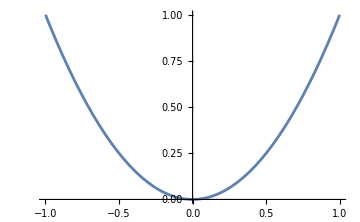

```mathematica
Plot[ f[x],{x,-1,1}]
```

```mathematica
(* A function defined using built-in elementary functions *)
```

```mathematica
f1[x_]:=Sin[x^2]+Cos[x]
```

```mathematica
(* Call f1 *)
```

```mathematica
f1[Pi]
```

-1+Sin[π^2]

```mathematica
(* Plot f1[x], where x ∈ [-14,15] *)
```

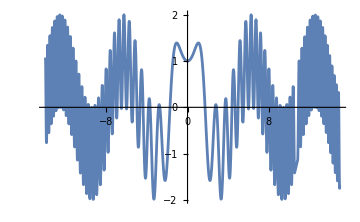

```mathematica
Plot[f1[x],{x,-14,15}]
```

```mathematica
(* Plot a list of functions. f1 defined above and f2[x] is defined by f2[x_]:=Sin[x]+6/(1+x^2)+f1[x]. 
The range of x for f1 and f2 is the same i.e. x∈[-10,15] *)
```

```mathematica
f2[x_]:=Sin[x]+6/(1+x^2)+f1[x]
```

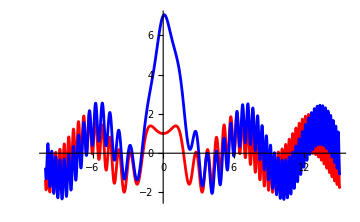

```mathematica
Plot[{f1[x],f2[x]},{x,-10,15},PlotStyle->{Red,Blue}] (* Plot 2 function / ตำแหน่งสีก็ตาม Function คล้าย ๆ Python *)
```

```mathematica
(* Plot a list of functions using the list of options *)
```

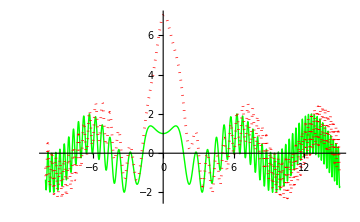

```mathematica
Plot[{f1[x],f2[x]},{x,-10,15},PlotStyle->{{Thick,Green},{Dotted,Red}}]
```

```mathematica
(* Plot several functions using colors defined by an RGB. Use a color for the background
Include the RGB from the menu: Insert->Color *)
```

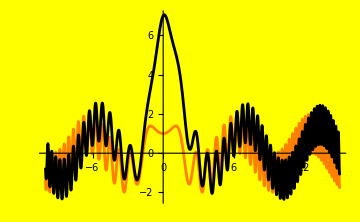

```mathematica
Plot[{f1[x],f2[x]},{x,-10,15},PlotStyle->{RGBColor[1,0.5,0],Black}, Background->Yellow]
```

```mathematica
(* Basics of Lists *)
```

```mathematica
(* Lists generate a collection of objects. As you will see later, 
lists are very important and general structures. They include numbers, functions, matrices, symbolic expressions 
and even images,  graphs and video. 
*)
```

```mathematica
(* A list of numbers (vector)  *)
```

```mathematica
A:={1,-5,3.4,9}
```

```mathematica
(* Extract the 4-th element of the list (double [[]]) คล้าย ๆ Array แต่ตัวแรกเริ่มต้นที่ 1 แหงล่ะ! *)
```

```mathematica
A[[4]]
```

9

```mathematica
(* One can apply the index directly to the list *)
```

```mathematica
(* Matrix *)
```

```mathematica
M1={{1,2,3},{5,6,7}}
```

{{1,2,3},{5,6,7}}

```mathematica
(* Matrix view *)
```

```mathematica
MatrixForm[M1]
```

(1 | 2 | 3
5 | 6 | 7)

```mathematica
(* Extract the element 21 (row=2, col=1) *)
```

```mathematica
M1[[2]][[1]]
```

5

```mathematica
(* An upcoming  lecture will introduce details of the lists *)
```

```mathematica
(* Functions of 2 or more variables *)
```

```mathematica
f2D[x_,y_]:=x^2+y^2 (* f2D เป็นชื่อ Function เฉย ๆ ไม่ได้ใช้ built-in function แต่อย่างใดเด้อ *)
```

```mathematica
(* Call the function with numerical arguments *)
```

```mathematica
f2D[2,5]
```

29

```mathematica
(* Plot the f2D. The range of x and y must be specified by the lists e.g. {x,-1,1},{y,-1,1} *)
```

```mathematica
Plot3D[f2D[x,y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
(* The arguments of the function can be represented by a list. อันนี้ Function เหมือนข้างบนเลย แต่แค่ Define คนละแบบ เผื่อมี argument เยอะ ๆ ก็ define โดยการใช้ List ได้ *)
```

```mathematica
f2DL[{x_,y_}]:=x^2+y^2
```

```mathematica
(* Call. Check the difference with f2D  *)
```

```mathematica
f2DL[{2,5}]
```

29

```mathematica
(* Define a list as the argument *)
```

```mathematica
ArgL={2,5}
```

{2,5}

```mathematica
f2DL[ArgL] (* Call function with one argument ได้เลย โดยมีค่าเป็น list อยู่ข้างใน ก็จะ evaluate ค่าออกมาให้ *)
```

29

```mathematica
Plot3D[f2DL[{x,y}],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
(* If one or both arguments are symbolic M14 generates a symbolic output  *)
```

```mathematica
Clear[a]
```

```mathematica
f2D[a,5]
```

25+a^2

```mathematica
f2D[1+a^2,Sqrt[1+a+a^2]]
```

1+a+a^2+(1+a^2)^2

```mathematica
(* Note the function "Simplify" ถ้าสมมติมี Function ที่ติดตัวแปลใช้ Simplify ให้มันดูง่ายขึ้นได้ *)
```

```mathematica
Simplify[f2D[1+a^2,Sqrt[1+a+a^2]]]
```

2+a+3 a^2+a^4

```mathematica
(* The arguments can be represented by the general list  a
The advantage is that a can include any number of elements
*)
```

```mathematica
fL[a_]:=a[[1]]^2+a[[2]]^2
```

```mathematica
(* The call and the plot of such a function is similar to f2DL*)
```

```mathematica
fL[{1,3}]
```

10

```mathematica
(* Define *)
```

```mathematica
ArgL={1,3}
```

{1,3}

```mathematica
(* Call *)
```

```mathematica
fL[ArgL]
```

10

```mathematica
(* Exceeding the number of arguments is ignored *)
```

```mathematica
fL[{1,3,5}]
```

10

```mathematica
ArgLExceed={1,3,67}
```

{1,3,67}

```mathematica
fL[ArgLExceed]
```

10

```mathematica
(* Generalization:  Transformation f[a_]:=b, where a and b are the lists *)
```

```mathematica
(* Example 1 f:R2->R2 *)
```

```mathematica
fT1[x_,y_]:={x^2+y,Sin[x^2-y]}
```

```mathematica
(* or equivalently  *)
```

```mathematica
fT2[a_]:={a[[1]]^2+a[[2]],Sin[a[[1]]^2-a[[2]]]} (* อันนี้ก็เหมือนเดิม แต่ทำให้มันมี argument ตัวเดียว แต่สุดท้ายก็ call list เข้ามาแล้วก็ access coorespond to each member เท่านั้นเอง *)
```

```mathematica
(* Call and plot fT1 and fT2  *)
```

```mathematica
fT1[2,7.]
```

{11.,-0.14112}

```mathematica
fT2[{2,7.}] (* have to call with one argument that's in a list format *)
```

{11.,-0.14112}

```mathematica
(* Functions F:R2->R2 can be displayed by vector fields (see the upcoming lectures). Alternatively the 2 components can be displayed on two independent graphs as follows  *)
```

```mathematica
PL1= Plot3D[fT2[{x,y}][[1]],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
PL2= Plot3D[fT2[{x,y}][[2]],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
(* Combine *)
```

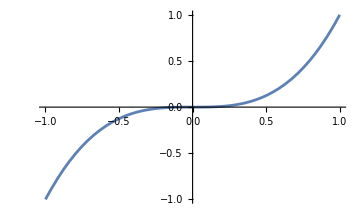
{-Graphics3D-,-Graphics3D-,-Graphics-}

```mathematica
PL={PL1,PL2, Plot[x^3, {x, -1, 1}]}
```

```mathematica
PL[[2]] (* เราก็สามารถ Access แบบนี้ได้ *)
```

-Graphics3D-

```mathematica
(* Any transformation F:R2->Rn or even f:Rm->Rn can be visualized the same way  *)
```

```mathematica
(* Example F:R2->R3, using the list of arguments *)
```

```mathematica
fT3[a_]:={a[[1]]^2+a[[2]],Sin[a[[1]]^2-a[[2]]], a[[1]]^2-a[[2]]^2}
```

```mathematica
{P1=Plot3D[fT3[{x,y}][[1]],{x,-1,1},{y,-1,1}],P2=Plot3D[fT3[{x,y}][[2]],{x,-1,1},{y,-1,1}],P3=Plot3D[fT3[{x,y}][[3]],{x,-1,1},{y,-1,1}]};
```

```mathematica
P123={P1,P2,P3}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(* Parametric function is a particular case of the transformation f:R->R2 and f:R->R3. 
Its geometric representation is a curve in 2D or 3D  *)
```

```mathematica
(* Parametric lines in R2 and R3 are familiar objects from the course of LA. (The DA will study them soon) *)
```

```mathematica
(* Define parametric lines in R2 *)
```

```mathematica
(* The direction vector  *)
```

```mathematica
DV={1,2}
```

{1,2}

```mathematica
(* The free term (intercept) *)
```

```mathematica
B={3,3}
```

{3,3}

```mathematica
(* The line equation is given by *)
```

```mathematica
L[t_]:=DV*t+B
```

```mathematica
(* Mathematica outputs the parametric format when we call L[t]*)
```

```mathematica
L[t]
```

{3+t,3+2 t}

```mathematica
(* Note the Matrix (Vector) form *)
```

```mathematica
MatrixForm[L[t]]
```

(3+t
3+2 t)

```mathematica
(* Parametric functions are displayed by ParametricPlot  *)
```

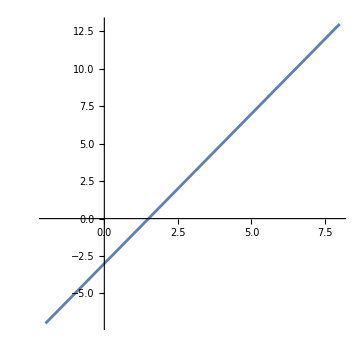

```mathematica
ParametricPlot[L[t],{t,-5,5},AspectRatio->1]
```

```mathematica
(* Define the parametric line as follows *)
```

```mathematica
Lx[t_]:=t+3
```

```mathematica
Ly[t_]:=2t+3
```

```mathematica
Lnew[t_]:={Lx[t],Ly[t]}
```

```mathematica
(* The graph shows the same line *)
```

```mathematica
ParametricPlot[Lnew[t],{t,-5,5},AspectRatio->1]
```

-Graphics-

```mathematica
(* A general (nonlinear) parametric function is defined using the same structure
i.e. the x and the y components of the function are defined separately 
and combined into a 2D vector-function (list)   *)
```

```mathematica
(* A circle with the radius R=3.5 *)
```

```mathematica
R=3.4
```

3.4

```mathematica
xt1[t_]:=R Cos[t]
```

```mathematica
yt1[t_]:=R Sin[t]
```

```mathematica
(* Define a vector-function *)
```

```mathematica
Cir[t_]:={xt1[t],yt1[t]}
```

```mathematica
(* Plot Cir  *)
```

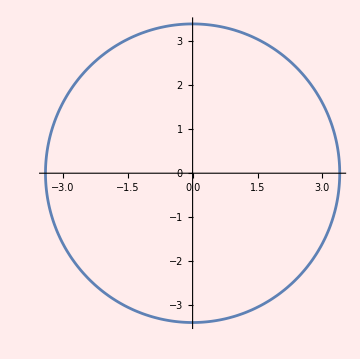

```mathematica
ParametricPlot[Cir[t],{t,0,2 Pi},Background->LightPink]
```

```mathematica
(* Spiral - the radius is a decreasing linear function of t *)
```

```mathematica
RC[t_]:=R(2Pi-t)/(2Pi) (* Change radius to be dynamic (linearly) *)
```

```mathematica
RC[0]
```

3.4

```mathematica
RC[2Pi]
```

0.

```mathematica
xt2[t_]:=RC[t]  Cos[t]
```

```mathematica
yt2[t_]:=RC[t] Sin[t]
```

```mathematica
Spi[t_]:={xt2[t],yt2[t]}
```

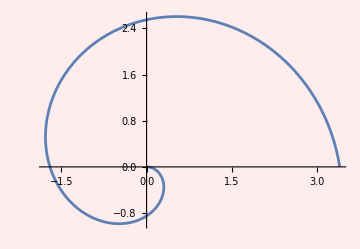

```mathematica
ParametricPlot[Spi[t],{t,0,2 Pi},Background->LightPink]
```

```mathematica
(* Plotting two parametric functions, specifying the colors *)
```

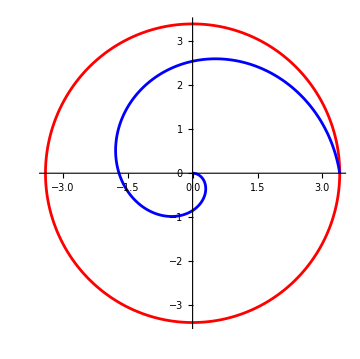

```mathematica
ParametricPlot[{Cir[t],Spi[t]},{t,0,2Pi}, PlotStyle->{Red,Blue}]
```

```mathematica
(* Increase the # of rounds of the spiral *)
```

```mathematica
RC1[t_]:=R(4Pi-t)/(4Pi)
```

```mathematica
RC1[0]
```

3.4

```mathematica
RC1[4Pi]
```

0.

```mathematica
xt21[t_]:=RC1[t] Cos[t]
```

```mathematica
yt21[t_]:=RC1[t] Sin[t]
```

```mathematica
Spi1[t_]:={xt21[t],yt21[t]}
```

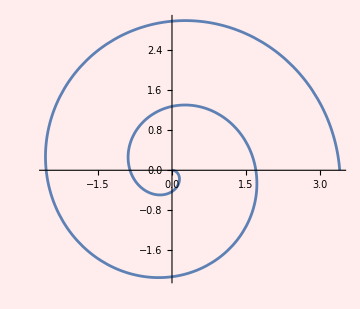

```mathematica
ParametricPlot[Spi1[t],{t,0,4 Pi},Background->LightPink]
```

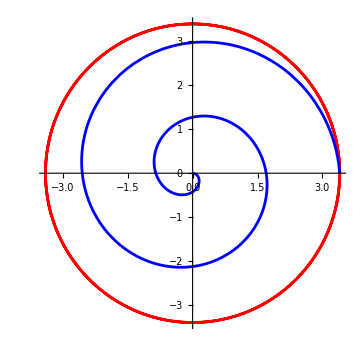

```mathematica
ParametricPlot[{Cir[t],Spi1[t]},{t,0,4Pi}, PlotStyle->{Red,Blue}]
```

```mathematica
(* Plotting three parametric functions, specifying the colors and the line type  *)
```

```mathematica
(* The Nephroid curve  *)
```

```mathematica
a=1
```

1

```mathematica
xN[t_]:=a(3Cos[t]-Cos[3t])
```

```mathematica
yN[t_]:=a(3Sin[t]-Sin[3t])
```

```mathematica
Nep[t_]:={xN[t],yN[t]}
```

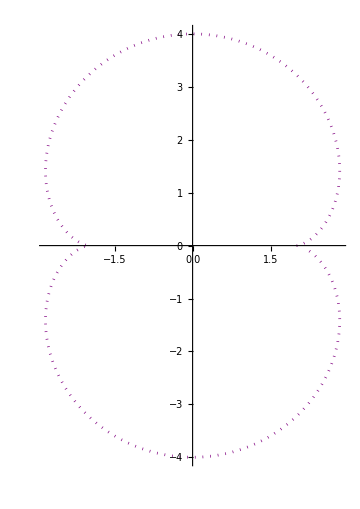

```mathematica
ParametricPlot[Nep[t],{t,0,6}, PlotStyle->{Purple, Dotted}]
```

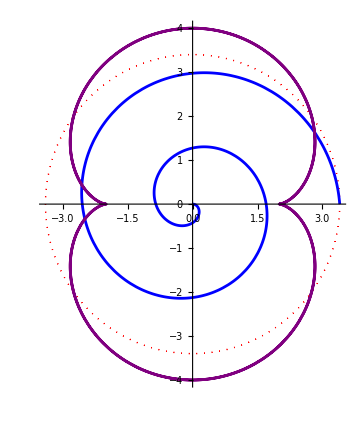

```mathematica
ParametricPlot[{Cir[t],Spi1[t],Nep[t]},{t,0,4Pi}, PlotStyle->{{Thick,Red,Dotted},Blue,Purple}]
```